# Copyright information

“STEcode.nb” provides they functions necessary to reproduce the results from “Symbolic transfer entropy reveals the age structure of pandemic influenza transmission from high-volume influenza-like illness data”, by SM Kissler, C Viboud, BT Grenfell, and JR Gog. 

Copyright (C) 2019, Stephen Kissler

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation,  version 3.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details.

You should have received a copy of the GNU General Public License along with this program. If not, see <http://www.gnu.org/licenses/>.

# SIR epidemic simulator:

SIRGillespie simulates a SIR epidemic for n age groups. 
Inputs:
	S0: Array (length n) with the number of susceptible individuals initially in each age group
	I0: Array (length n) with the number of infected individuals initially in each age group
	β: Matrix (nxn) of transmission rates such that the i,j^th entry is the transmission constant from group j to group i
	γ: Scalar recovery rate, or inverse of the infectious period
	maxits: Maximum number of iterations to run the algorithm
	maxt: Maximum number of time steps to run the epidemic

```mathematica
SIRGillespie[S0_,I0_,β_,γ_,maxits_,maxt_] := Module[{nclass,NN, SS, II,t,SSTransitions, IITransitions, infrates, recrates, totrate, τ,ratelist, cumratelist, draw, event, SSnew, IInew},

(*--- Initialize the simulation --- *)
If[Length[S0]≠ Length[I0], Print["Error"]; Return[]];(*if the vectors don't have the same length, and so don't specify the same number of age classes, then the simulation can't continue*)
nclass = Length[S0];(*specify the number of age classes there are*)
NN = Total[S0] + Total[I0]; (*calculate the total population size*)
SS = {S0}; (*initialize an array of susceptible counts*)
II = {I0}; (*initialize an array of infected counts*)
t = {0}; (*initialize an array to store time points*)
SSTransitions = Join[DiagonalMatrix[ConstantArray[-1, nclass]],ConstantArray[ConstantArray[0,nclass],nclass]]; (*Generate an array of the possible S-related transitions (first infection, then recovery)*)
IITransitions = Join[DiagonalMatrix[ConstantArray[1, nclass]],DiagonalMatrix[ConstantArray[-1, nclass]]];(*Generate an array of the possible I-related transitions (first infection, then recovery)*)

(*--- Begin iterating through the simulation --- *)
Do[
infrates = 1/NN*DiagonalMatrix[SS⟦it⟧].β.II⟦it⟧; (*Calculate infection rates for each class*)
recrates = γ*II⟦it⟧; (*Calculate recovery rates for each class*)
totrate = Total[infrates] + Total[recrates]; (*Calculate the total rate of any event occurring*)

(*--- Calculate the time to next transition ---*)
If[totrate==0, (*If the event rate is 0, then the simulation must be over*)
Return[{SS, II,t}], (*Return the output vectors*)
τ = RandomVariate[ExponentialDistribution[totrate]]; (*Otherwise, draw the next event's time from an exponential distribution*)
];

(*--- Identify the transition ---*)
ratelist = Join[infrates, recrates]/totrate; (*Calculate the probability of each event occurring*)
cumratelist = Table[Total[ratelist⟦Range[1,i]⟧],{i,Length[ratelist]}];(*Turn these probabilities into a vector of cumulative probabilities*)
draw = RandomVariate[UniformDistribution[]]; (*Draw a random uniform variable for choosing the event*)
event = Flatten[Position[cumratelist, _?(#>draw&)]]⟦1⟧; (*Pick the event, based on the cumulative probability distribution*)
SSnew = SS⟦it⟧ + SSTransitions⟦event⟧; (*Update the number of susceptibles*)
IInew = II⟦it⟧ + IITransitions⟦event⟧; (*Update the number of infecteds*)
SS = Join[SS, {SSnew}]; (*Update the 'susceptible' output vector*)
II = Join[II, {IInew}]; (*Update the 'infected' output vector*)
t = Join[t,{t⟦it⟧+τ}]; (*Update the 'event times' output vector*)
If[t⟦it⟧+τ > maxt, Return[{SS, II,t}]]; (*If we've exceeded the maximum amount of time allowed for the simulation, return the output vectors*)
,{it, maxits}];
Return[{SS, II,t}]; (*If we've reached this point, we've reached the maximum number of iterations. Return the output.*)
]
```

# SIR demonstration:

Generate SIR simulations for two age classes strongly driven by age class 1 (relative reproduction matrix {{4,1},{2,1}}).

```mathematica
k = 1; (*Define the strength of driving from age group 1, between 0 and 1*)
rrepmat = {{1+3 k,1},{1 + k,1}}; (*define the relative reproduction matrix*)
R0 = 1.5;  (*fix R0. NOTE! this is not the intial recovered, but the basic reproduction number*)
γ = N[1/7]; (*recovery rate*)
maxits = 5000; (*max number of iterations to run each Gillespie simulation*)
nepidemics = 5; (*fix the number of (successful) outbreaks to run*)
binwidth = 7; (*number of days to bin gillespie output into (7 = weekly bins, 3.5 = half-weekly bins)*)
noisefraction = .005; (*what fraction of the population gets random respiratory illness each week*)
maxt = 175; (*longest time to run the epidemic for*)
pvec = {0.5, 0.5}; (*vector of the fractional percentages of the population made up by each age group*)
nclasses = 2;
β = (2 γ R0)/(2 + 3 k + √(9 k^2 + 4 k + 4))*DiagonalMatrix[1/pvec].rrepmat; (*the transmission matrix*)
ngm = 1/γ*DiagonalMatrix[pvec].β; (*calculate the next generation matrix from the elements defined above*)
IImat = ConstantArray[0,{nclasses,nepidemics,Floor[maxt/binwidth]}];
successes = 0; (*initialize a variable to store how many epidemics have taken off*)
While[successes < nepidemics,
draw = RandomReal[]; (*Draw a random variable to determine in which group the epidemic starts*)
If[draw>0.5, I0 = {1,0};S0 = {499,500},(*else*) I0 = {0,1}; S0 = {500,499}];
{SS, II,t} = SIRGillespie[S0,I0,β,γ,maxits, maxt];(*Simulate the epidemic*)
ncases = Total[Table[Count[Drop[II⟦All,c⟧,1] - Drop[II⟦All,c⟧,-1] ,_?(#>0&)],{c, nclasses}]]; (*Count the total number of infections*)
If[ncases>100, (*if the epidemic has proceeded for sufficient time*)
successes = successes + 1; (*Record the epidemic as a success*)
binindices = Table[
Flatten[Position[t,_?(#≥i*binwidth && #<(i+1)*binwidth&)]],{i,0,Ceiling[(maxt-binwidth)/binwidth]}]; (*Generate a set of indices for the incidence bins*)
noise = Table[Table[RandomVariate[PoissonDistribution[noisefraction*(S0⟦i⟧+I0⟦i⟧)]],{i,nclasses}],{Length[binindices]}]; (*Calculate the amount of noise in each bin*)
binnedinfections = Table[
If[Length[SS⟦binindices⟦i⟧⟧]>0,
SS⟦binindices⟦i⟧⟧⟦1⟧ - SS⟦binindices⟦i⟧⟧⟦-1⟧,
ConstantArray[0,Length[SS⟦1⟧]]]
,{i,Length[binindices]}] + noise; (*Bin the infections, with noise*)
Do[
IImat⟦i,successes⟧ = binnedinfections⟦Range[1,Floor[maxt/binwidth]],i⟧; (*Clean up the infected array*)
,{i,nclasses}]
];
];
```

Plot the output:

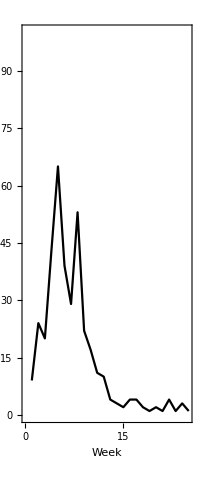
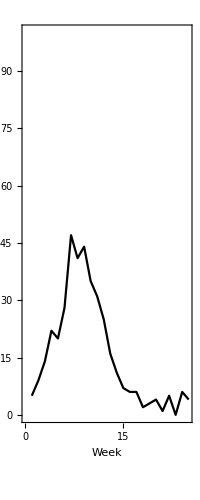
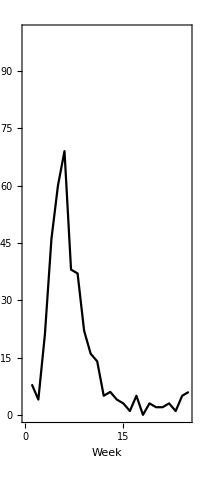
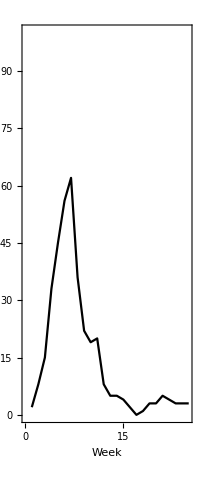
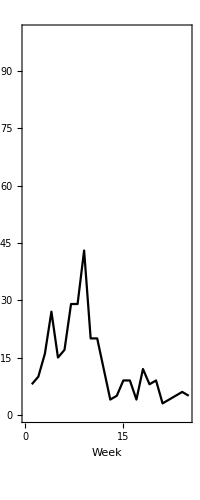
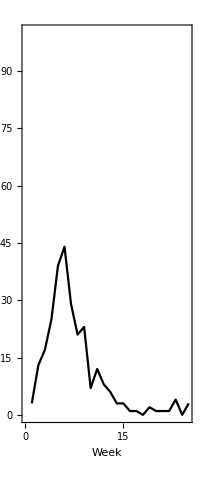
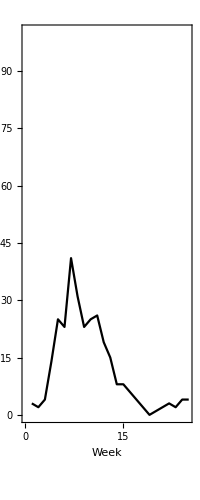
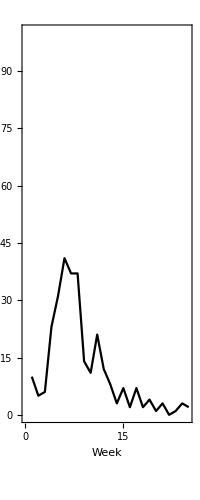
Cases, Group I | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Cases, Group J | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
Join[{Style[Rotate["Cases, Group I",π/2],FontSize->20,FontFamily->"Helvetica"]},Table[
ListLinePlot[
IImat⟦1,i⟧,
Frame->{True,True,False,False},
FrameTicks->{Table[{i, Rotate[ToString[i],π/2]},{i,0,25,5}],Automatic},
FrameLabel->{"Week", None},
PlotStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,100}, AspectRatio->Full
]
,{i,1,nepidemics}]],
Join[{Style[Rotate["Cases, Group J",π/2],FontSize->20,FontFamily->"Helvetica"]},Table[
ListLinePlot[
IImat⟦2,i⟧,
Frame->{True,True,False,False},
FrameTicks->{Table[{i, Rotate[ToString[i],π/2]},{i,0,25,5}],Automatic},
FrameLabel->{"Week", None},
PlotStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,100}, AspectRatio->Full
],{i,1,nepidemics}]]
},Dividers->All,Spacings->1, ItemSize->Full]
```

# Poisson epidemic simulator:

PoissonSim simulates a Poisson-style epidemic for n age groups. 
Inputs:
	initinf: Vector containing the initial number of infecteds in each age group.
	genlength: Generation interval of transmission
	epilength: Length of time to run the outbreak
	changepoint: Time point at which transmission changes from being governed by NGMHigh to NGMLow
	NGMHigh: The high-reproduction next-generation matrix
	NGMLow: The low-reproduction next-generation matrix
	gensperbin: Number of generations to put into each bin

```mathematica
(*Generate a function to easily draw Poisson random variables*)
RPoisson[μ_] := If[μ>0, RandomVariate[PoissonDistribution[μ]],0];
```

```mathematica
PoissonSim[initinf_, genlength_, epilength_, changepoint_, NGMHigh_, NGMLow_, gensperbin_]:=Module[{ngens, ivec, binvec},
(* calculate how many generations are in the outbreak: *)
ngens = Ceiling[epilength/genlength];
(* initialize vector of infecteds: *)
ivec = {initinf};
(* run the simulation *)
Table[ivec = Join[ivec, 
If[it*genlength≤changepoint, (*if we're before the changepoint,*)
{RPoisson/@(NGMHigh.ivec⟦-1⟧)}, (*iterate using NGMHigh x previous infected*)
{RPoisson/@(NGMLow.ivec⟦-1⟧)} (*else, iterate using NGMLow x previous infected*)
]
],{it, ngens}];
binvec = Total/@Partition[ivec,gensperbin]; (*bin the observed infections*)
Return[binvec];
]
```

# Poisson demonstration:

```mathematica
RHigh = 1.5; (*Set the high effective reproduction number*)
RLow =0.8; (*Set the low effective reproduction number*)
ivecfull = {}; (*Initialize a vector for the simulated output*)
NGMstruct={{4,1},{2,1}}; (*Set the relative reproduction matrix*)
NGMHigh = RHigh*N[NGMstruct / Max[Eigenvalues[NGMstruct]]]; (*Set the 'high-R' NGM*)
NGMLow = RLow*N[NGMstruct / Max[Eigenvalues[NGMstruct]]]; (*Set the 'low-R' NGM*)
changepoint = 28; (*number of generations after which to switch to the RLow*)
epilength = 175; (*length of epidemic in days*)
gensperbin = 2; (*number of generations per bin*)
genlength = 3.5; (*length of generation interval in days*)
noiserate =10; (*amount of noise to inject into each category, in each bin*)
nepidemics = 5; (*number of epidemics per STE calculation*)
(* RUN THE EPIDEMIC SIMULATION *)
While[Length[ivecfull]< nepidemics,
draw = RandomReal[];
If[draw>0.5, initinf = {1,0}, initinf = {0,1} ];
ivec = PoissonSim[initinf, genlength, epilength, changepoint, NGMHigh, NGMLow,gensperbin];
If[Total[Flatten[ivec]]>100, (*check that at least 100 people were infected*)
ivecnoisy = ivec +  RandomVariate[PoissonDistribution[noiserate], {Length[ivec],Length[NGMHigh]}];
ivecfull = Join[ivecfull, {ivecnoisy}]
];
];
```

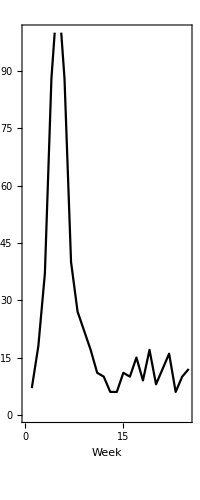
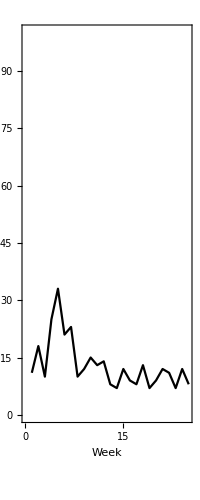
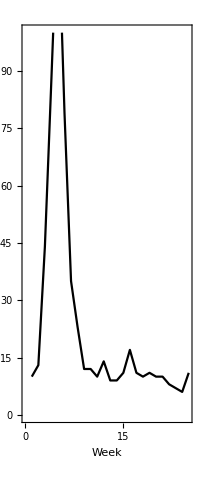
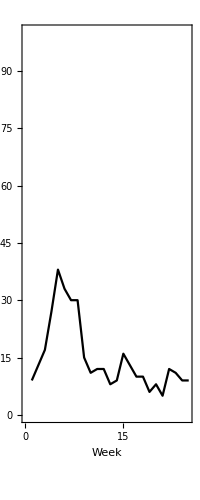
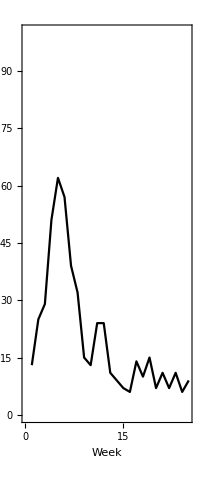
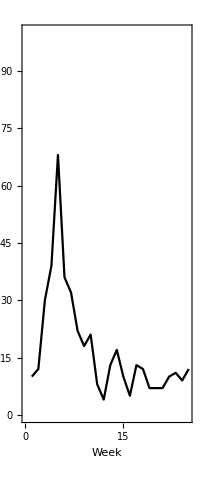
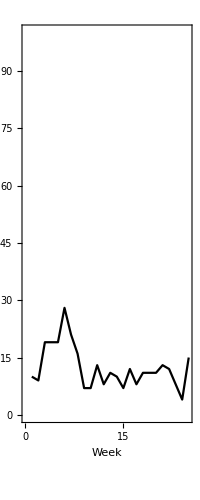
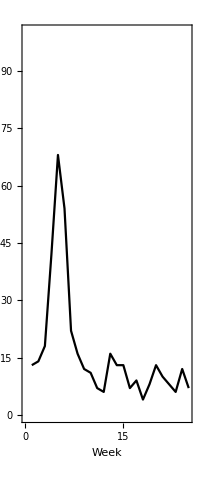
Cases, Group I | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Cases, Group J | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
Join[{Style[Rotate["Cases, Group I",π/2],FontSize->20,FontFamily->"Helvetica"]},Table[
ListLinePlot[
ivecfull⟦i,All,1⟧,
Frame->{True,True,False,False},
FrameTicks->{Table[{i, Rotate[ToString[i],π/2]},{i,0,25,5}],Automatic},
FrameLabel->{"Week", None},
PlotStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,100}, AspectRatio->Full
]
,{i,1,nepidemics}]],
Join[{Style[Rotate["Cases, Group J",π/2],FontSize->20,FontFamily->"Helvetica"]},Table[
ListLinePlot[
ivecfull⟦i,All,2⟧,
Frame->{True,True,False,False},
FrameTicks->{Table[{i, Rotate[ToString[i],π/2]},{i,0,25,5}],Automatic},
FrameLabel->{"Week", None},
PlotStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,100}, AspectRatio->Full
],{i,1,nepidemics}]]
},Dividers->All,Spacings->1, ItemSize->Full]
```